```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DD[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,Log[2,n]}]
P[n_,k_,s_]:=P[n,k,s]=Sum[ j^-s K[j]P[Floor[n/j],k-1,s],{j,2,n}];P[n_,0,s_]:=1
DDa[n_, z_] := Sum[ z^k/k! P[n,k],{k,0,Log[2,n]}]
DDa[n_, z_,s_] := Sum[ z^k/k! P[n,k,s],{k,0,Log[2,n]}]
DDa2[n_, z_] := Sum[ z^k/k! P[n,k]/z,{k,0,Log[2,n]}]
Dhyp[n_,k_,a_,s_]:=Dhyp[n,k,a,s]=Sum[Binomial[k,j] Dhyp[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
StrictDivisorsHyperbola[A_,k_,n_,s_]:=Sum[((m^A)^(k-j)) Binomial[k,j] StrictDivisorsHyperbola[A,j,n/(m^(k-j)),m+1],{m,s,n^(1/k)},{j,0,k-1}]
StrictDivisorsHyperbola[A_,1,n_,s_]:=Sum[j^A,{j,s,n}]
StrictDivisorsHyperbola[0,1,n_,s_]:=Floor[n]-s+1
StrictDivisorsHyperbola[1,1,n_,s_]:=Floor[n](Floor[n]+1)/2-s (s-1)/2
StrictDivisorsHyperbola[2,1,n_,s_]:=Floor[n](Floor[n]+1)(2Floor[n]+1)/6-(s-1)s (2s-1)/6
StrictDivisorsHyperbola[3,1,n_,s_]:=Floor[n]^2(Floor[n]+1)^2/4-s^2(s-1)^2/4
StrictDivisorsHyperbola[A_,0,n_,s_]:=1
SumPrimesHyperbola[A_,n_]:=Sum[(-1)^(k+1)/(j k) MoebiusMu[j]StrictDivisorsHyperbola[j A,k,n^(1/j),2],{j,1,Log[2,n]},{k,1,Log[2,(n^(1/j))]}]
DDD[n_,z_,s_]:=Expand[Sum[bins[z,a] StrictDivisorsHyperbola[-s,a,n,2],{a,0,Log[2,n]}]]
lin[n_,s_] := Sum[ (-1)^(k+1)/k StrictDivisorsHyperbola[-s,k,n,2],{k,1,Log[2,n]}]
```

```mathematica
(-1/List@@NRoots[ DDD[1112601,x,-2]==0,x][[All,2]])
```

{0.0026846,0.0337774,0.00339989-0.0177528 ⅈ,0.00339989+0.0177528 ⅈ,0.0129288-0.0338084 ⅈ,0.0129288+0.0338084 ⅈ,0.0418972-0.0687773 ⅈ,0.0418972+0.0687773 ⅈ,0.0521515-0.0938085 ⅈ,0.0521515+0.0938085 ⅈ,0.129722-0.178989 ⅈ,0.129722+0.178989 ⅈ,0.275047-0.19972 ⅈ,0.275047+0.19972 ⅈ,0.536214-0.164698 ⅈ,0.536214+0.164698 ⅈ,1.0008,3.38194×10^16,-0.0000911672-0.00160732 ⅈ,-0.0000911672+0.00160732 ⅈ}

```mathematica
N[lin[1112601,-2]]
```

3.38194×10^16

```mathematica
NumberForm[3.381939745558961*^16,ExponentFunction->(If[-20<#<20,Null,#]&)]
NumberForm[3.3819397455589616*^16,ExponentFunction->(If[-20<#<20,Null,#]&)]
```

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

33819397455589600.

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

33819397455589620.

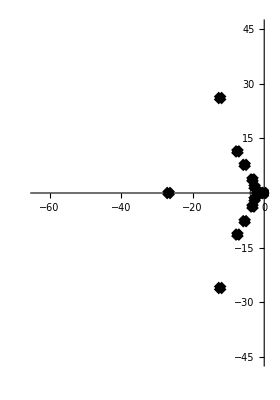

```mathematica
RootLocusPlot[1/Expand[DDD[1112600,x,0]],{k,0,1},FeedbackType->None]
```

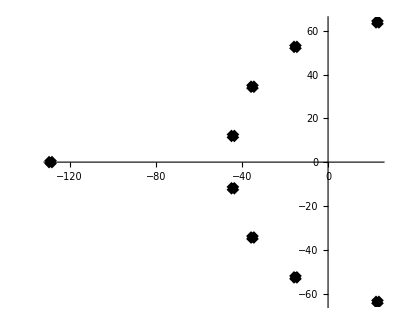

```mathematica
RootLocusPlot[1/Expand[DDD[1000,x,4]],{k,0,1},FeedbackType->None]
```

```mathematica
N[DDD[1000,z,4]]
```

1.+0.0791099 z+0.00312919 z^2+0.0000825164 z^3+1.63192×10^-6 z^4+2.58075×10^-8 z^5+3.3842×10^-10 z^6+3.65863×10^-12 z^7+3.02665×10^-14 z^8+1.11392×10^-16 z^9

```mathematica
(List@@NRoots[ DDD[1000,x,4]==0,x][[All,2]])
```

{-128.827,-44.1698-11.9556 ⅈ,-44.1698+11.9556 ⅈ,-35.0862-34.4187 ⅈ,-35.0862+34.4187 ⅈ,-15.125-52.6184 ⅈ,-15.125+52.6184 ⅈ,22.9387-63.7958 ⅈ,22.9387+63.7958 ⅈ}

```mathematica
(N[D[DDD[100,z,s],s]]/.s->0)
```

-94.0453 z-169.15 z^2-81.6195 z^3-17.6846 z^4-1.19616 z^5-0.0438125 z^6

```mathematica
(List@@NRoots[(N[D[DDD[100,z,s],s]]/.s->0)==0,z][[All,2]])
```

{-10.6971-12.1994 ⅈ,-10.6971+12.1994 ⅈ,-2.53645-1.82621 ⅈ,-2.53645+1.82621 ⅈ,-0.834706,0.}

```mathematica
vv:={-10.697109591508221-12.19935485425952 ⅈ,-10.697109591508221+12.19935485425952 ⅈ,-2.5364503360079835-1.8262103341135916 ⅈ,-2.5364503360079835+1.8262103341135916 ⅈ,-0.8347063543903029}
```